# Iteration 4.1: Modelling Resource-Limited Farmer-Warrior Dynamics

## with Famine Thresholds and Non-Negative Food Reserves

*See warrior population decreases as food consumption increases relative to famers, due to needing more farmers to maintain the population. Food resources will never go to 0 exactly due to being interdependant ratio.

```mathematica
(*System Diagram:Farmers,Warriors,and Food Flow*)systemGraph=Graph[{"Farmers (Nf)"->"Food Reserves (F)","Food Reserves (F)"->"Warriors (Nw)","Farmers (Nf)"->"Warriors (Nw)","Warriors (Nw)"->"Food Reserves (F)"},GraphStyle->"FlowChart",VertexLabels->Placed["Name",Center],ImageSize->Large];
systemGraph
```

-Graphics-

```mathematica
(* Parameter Relationships as Causal Network *)

parameterGraph = Graph[
   {
    "Food Production Rate (α)" -> "Food Reserves (F)",
    "Food Reserves (F)" -> "Farmers (Nf)", 
    "Food Reserves (F)" -> "Warriors (Nw)",
    "Resource Consumption Rate (β)" -> "Food Reserves (F)",
    "Warrior Recruitment Rate (σ)" -> "Farmers (Nf)",
    "Warrior Recruitment Rate (σ)" -> "Warriors (Nw)",
    "Famine Death Increase (ϵ)" -> "Farmers (Nf)",
    "Famine Death Increase (ϵ)" -> "Warriors (Nw)"
   },
   GraphStyle -> "CausalLoop", 
   VertexLabels -> Placed["Name", Center], 
   ImageSize -> Large
];
parameterGraph
```

-Graphics-

```mathematica
-Graphics--Graphics-
```

```mathematica
(*Population Dynamics Equations with Non-Negative Food Reserves*)
farmerWarriorUpdate=Function[{state,alpha,beta,gamma,delta,lambda,sigma,theta,epsilon},
Module[
{
F=state[[1]],
Nf=state[[2]],
Nw=state[[3]],
gammaEff,
deltaEff,
dFdt
},
(*Ensure non-negative food*)
F=Max[F,0];

(*Adjust death rates during famine*) 
gammaEff=If[
F<=0,
gamma+epsilon,
gamma];

(*Food dynamics with non-negative enforcement*)
deltaEff=If[ 
F<=0,
delta+epsilon,
delta
];

dFdt=alpha Nf-beta (Nf+Nw);

dFdt=If[
F+dFdt<0,
-F,
dFdt
];

{
dFdt,(*dF/dt*)

(*dNf/dt*)
-If[
F>theta,
sigma Nf,
0
]-gammaEff Nf+lambda F/(1+F),

(*dNw/dt*)
If[
F>theta,
sigma Nf,
0
]-deltaEff Nw 
}]];

(*RK4(5) Integration Function*)
rk45FarmersWarriors=Function[{f,h,state},Module[{k1,k2,k3,k4,k5,k6,newState},k1=f[state];
k2=f[state+h k1/4];
k3=f[state+h (3 k1+9 k2)/32];
k4=f[state+h (1932 k1-7200 k2+7296 k3)/2197];
k5=f[state+h (439 k1/216-8 k2+3680 k3/513-845 k4/4104)];
k6=f[state+h (-8 k1/27+2 k2-3544 k3/2565+1859 k4/4104-11 k5/40)];
newState=state+h (16 k1/135+6656 k3/12825+28561 k4/56430-9 k5/50+2 k6/55);
(* Food is non-negative*)newState[[1]]=Max[newState[[1]],0];
newState]];

(*Simulation Function*)
simulateFarmersWarriors=Function[
{alpha,beta,gamma,delta,lambda,sigma,theta,epsilon,stepSize,tMax,F0,Nf0,Nw0},
Module[
{initialState,steps,results,f},

initialState={F0,Nf0,Nw0};

steps=Range[0,tMax,stepSize];

f=Function[state,farmerWarriorUpdate[state,alpha,beta,gamma,delta,lambda,sigma,theta,epsilon]];

results=NestList[rk45FarmersWarriors[f,stepSize,#]&,initialState,Length[steps]-1];

{steps,Transpose[results]}
]];

(*Phase Diagram with StreamPlot*)
plotPhaseDiagram=Function[{alpha,beta,gamma,delta,lambda,sigma,theta,epsilon,stepSize,tMax,F0,Nf0,Nw0},
Module[
{timeData,data,vectorField},
{timeData,data}=simulateFarmersWarriors[alpha,beta,gamma,delta,lambda,sigma,theta,epsilon,stepSize,tMax,F0,Nf0,Nw0];
vectorField=Function[
{F,Nf},
{alpha Nf-beta (Nf+Nw0),
-If[F>theta,sigma Nf,0]-gamma Nf+lambda F/(1+F)
}
];
Show[StreamPlot[vectorField[
F,
Nf
],
{F,0,500},
{Nf,0,100},
StreamStyle->Arrowheads[Small],Frame->True,FrameLabel->{
"Food Reserves (F)",
"Farmers (Nf)"
},PlotRange->{{0,500},{0,100}},AspectRatio->2/3],Graphics[{Thick,Red,Line[Transpose[{data[[1]],data[[2]]}]]}]]]];

(*Manipulate Block with Non-Negative Food Reserves*)
Manipulate[
Module[
{data,timeData,phasePlot},

{timeData,data}=simulateFarmersWarriors[alpha,beta,gamma,delta,lambda,sigma,theta,epsilon,stepSize,tMax,F0,Nf0,Nw0];

phasePlot=plotPhaseDiagram[alpha,beta,gamma,delta,lambda,sigma,theta,epsilon,stepSize,tMax,F0,Nf0,Nw0];

Column[
{
ListLinePlot[Transpose[{timeData,data[[1]]}],PlotRange->All,PlotStyle->Blue,Frame->True,FrameLabel->{"Time","Food Reserves (F)"},ImageSize->Large],
ListLinePlot[{
Transpose[{timeData,data[[2]]}],
Transpose[{timeData,data[[3]]}]},
PlotRange->All,PlotStyle->{Green,Red},Frame->True,
FrameLabel->{"Time","Population"},
PlotLegends->{"Farmers (Nf)","Warriors (Nw)"},
ImageSize->Large
],
phasePlot}]],

{{alpha,1.,"Food Production Rate (α)"},0.1,3.,0.1},
{{beta,0.5,"Food Consumption Rate (β)"},0.1,2.0,0.1},
{{gamma,0.01,"Farmer Death Rate (γ)"},0.001,0.1,0.001},
{{delta,0.02,"Warrior Death Rate (δ)"},0.01,0.2,0.01},
{{lambda,1.0,"Birth Rate (λ)"},0.1,3.0,0.1},
{{sigma,0.1,"Warrior Recruitment Rate (σ)"},0.01,0.5,0.01},
{{theta,200,"Food Threshold for War (θ)"},50,500,10},
{{epsilon,0.05,"Famine Death Rate Increase (ϵ)"},0.01,0.2,0.01},
{{F0,100,"Initial Food Reserves (F₀)"},50,300,10},
{{Nf0,80,"Initial Farmers (Nf₀)"},30,150,10},
{{Nw0,20,"Initial Warriors (Nw₀)"},0,50,5},
{{stepSize,0.1,"Step Size"},0.001,1.0,0.001},
{{tMax,150,"Total Time"},10,300,10},

ControlPlacement->Left,SaveDefinitions->True]
```

### Increasing Food consumption to see explain behaviour (each screenshot is increasing in consumption)

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

# Iteration 4.2: Ensemble Simulation of Food consumption

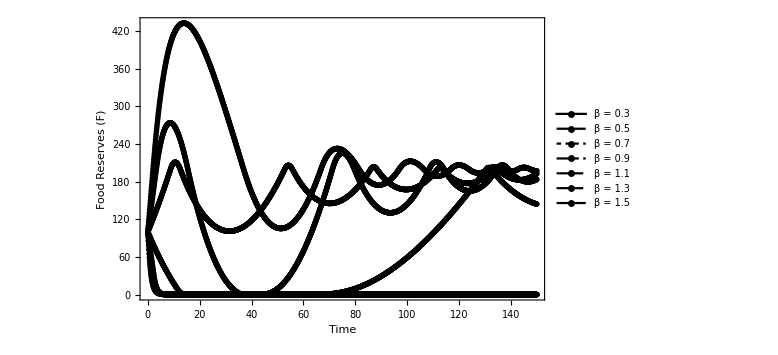

```mathematica
ClearAll["Global`*"];

(* Population Dynamics Equations with Non-Negative Food Reserves *)
farmerWarriorUpdate = 
  Function[{state, alpha, beta, gamma, delta, lambda, sigma, theta, 
    epsilon},
   Module[
    {F = state[[1]], Nf = state[[2]], Nw = state[[3]], gammaEff, 
     deltaEff, dFdt},
    (* Ensure non-negative food *)
    F = Max[F, 0];
    (* Adjust death rates during famine *)
    gammaEff = If[F <= 0, gamma + epsilon, gamma];
    deltaEff = If[F <= 0, delta + epsilon, delta];
    (* Food dynamics with non-negative enforcement *)
    dFdt = alpha Nf - beta (Nf + Nw);
    dFdt = If[F + dFdt < 0, -F, dFdt];
    {
     dFdt, (* dF/dt *)
     -If[F > theta, sigma Nf, 0] - gammaEff Nf + lambda F/(1 + F), 
     (* dNf/dt *)
     If[F > theta, sigma Nf, 0] - deltaEff Nw (* dNw/dt *)
     }
    ]
   ];

(* RK4(5) Integration Function *)
rk45FarmersWarriors = 
  Function[{f, h, state}, 
   Module[{k1, k2, k3, k4, k5, k6, newState}, 
    k1 = f[state];
    k2 = f[state + h k1/4];
    k3 = f[state + h (3 k1 + 9 k2)/32];
    k4 = f[state + h (1932 k1 - 7200 k2 + 7296 k3)/2197];
    k5 = 
     f[state + h (439 k1/216 - 8 k2 + 3680 k3/513 - 845 k4/4104)];
    k6 = 
     f[state + 
       h (-8 k1/27 + 2 k2 - 3544 k3/2565 + 1859 k4/4104 - 
           11 k5/40)];
    newState = 
     state + 
      h (16 k1/135 + 6656 k3/12825 + 28561 k4/56430 - 9 k5/50 + 
         2 k6/55);
    (* Ensure food remains non-negative *)
    newState[[1]] = Max[newState[[1]], 0];
    newState]];

(* Simulation Function *)
simulateFarmersWarriors = 
  Function[{alpha, beta, gamma, delta, lambda, sigma, theta, epsilon, 
    stepSize, tMax, F0, Nf0, Nw0},
   Module[{initialState, steps, results, f},
    initialState = {F0, Nf0, Nw0};
    steps = Range[0, tMax, stepSize];
    f = Function[state, 
      farmerWarriorUpdate[state, alpha, beta, gamma, delta, lambda, 
       sigma, theta, epsilon]];
    results = 
     NestList[rk45FarmersWarriors[f, stepSize, #] &, initialState, 
      Length[steps] - 1];
    {steps, Transpose[results]}
    ]];

(* Ensemble Simulation for Multiple Food Consumption Rates *)
ensembleResults = 
  Table[
   {
    beta, 
    simulateFarmersWarriors[
     1.0, beta, 0.01, 0.02, 1.0, 0.1, 200, 0.05, 0.1, 150, 100, 80, 
     20
     ][[2, 1]] (* Extract time-series of F *)
    },
   {beta, 0.3, 1.5, 0.2} (* Vary beta from 0.3 to 1.5 in steps of 0.2 *)
   ];

(* Plot the Results *)
ListLinePlot[
 Table[
  Transpose[{Range[0, 150, 0.1], ensembleResults[[i, 2]]}], 
  {i, Length[ensembleResults]}
 ],
 PlotRange -> All, 
 Frame -> True, 
 FrameLabel -> {"Time", "Food Reserves (F)"}, 
 PlotLegends -> 
  Table["β = " <> ToString[ensembleResults[[i, 1]]], {i, 
    Length[ensembleResults]}], 
 ImageSize -> Large
]
```

# Iteration 4.2: Bifurcation Due to Policy Changes (reaching)

## Lord has been tasked with writing policy (oh no)

## Refer to code comments for more nuanced explanations

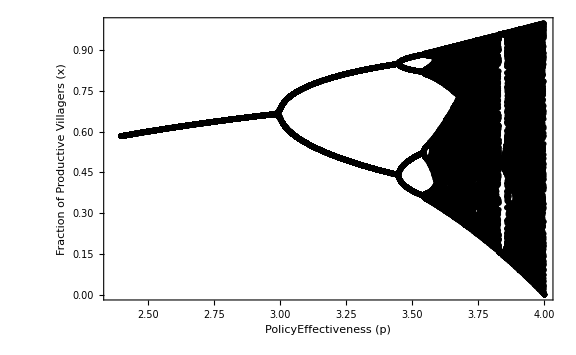

```mathematica
ClearAll["Global`*"];

(*We have called 'r' 'PolicyEffectiveness' to represent how changes in policy (resource management,training incentives,conscription relaxation) affect the productive population fraction.*)

productiveMap[x_,PolicyEffectiveness_]:=PolicyEffectiveness*x*(1-x)

(*x represents the fraction of villagers remaining productive after a season.PolicyEffectiveness (analogous to'r') is a parameter controlled by the lord’s decisions.*)

numIter=200;    (*total iterations per PolicyEffectiveness value*)
discard=100;    (*discard initial transient iterations*)
policyValues=Range[2.4,4,0.002]; (*Explore a range of PolicyEffectiveness values*)

bifData=Reap[Do[Module[{x=0.5},(*We start with a fraction of 0.5 as an initial condition*)
(*Now we let the system settle*)
Do[x=productiveMap[x,p],{numIter}];

(*Record the steady state values after discarding the transient*)
Do[x=productiveMap[x,p];
Sow[{p,x}],
{numIter-discard}]
],
{p,policyValues}]][[2,1]];

(*Now we have bifurcation data of how the fraction x varies as we change PolicyEffectiveness p*)

ListPlot[
bifData,
PlotRange->All,
Frame->True,
FrameLabel->{
"PolicyEffectiveness (p)",
"Fraction of Productive Villagers (x)"},
PlotStyle->{PointSize[0.001],Black},ImageSize->Large,Axes->False]
```

# Iteration 4.3: Modelling Chaotic Behaviour in due to policy

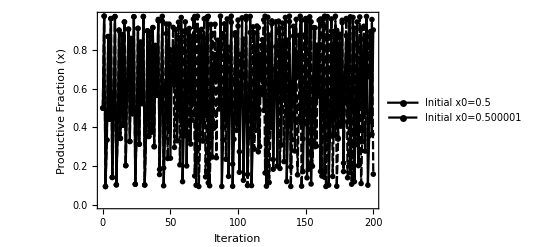

0.496413

```mathematica
ClearAll["Global`*"];

(*The logistic map*)
logisticMap[x_,r_]:=r x (1-x)

(*Parameter in chaotic regime*)
p=3.9;

(*Two initial conditions very close to each other*)
x0a=0.5;
x0b=0.500001;

numIter=200;
resA=Reap[Module[{xa=x0a},Sow[{0,xa}];
Do[xa=logisticMap[xa,p];
Sow[{n,xa}],{n,1,numIter}]]][[2,1]];

resB=Reap[Module[{xb=x0b},Sow[{0,xb}];
Do[xb=logisticMap[xb,p];
Sow[{n,xb}],{n,1,numIter}]]][[2,1]];

(*Plot both trajectories*)
ListLinePlot[{resA,resB},Frame->True,FrameLabel->{"Iteration","Productive Fraction (x)"},PlotLegends->{"Initial x0=0.5","Initial x0=0.500001"}]

(*Notice how they start very close but may diverge as iterations increase in the chaotic regime.*)

(*Compute Lyapunov exponent for logistic map at r=p*)

lyapunovExponent[r_,x0_,nmax_]:=Module[{x=x0,sum=0},Do[x=logisticMap[x,r];
(*derivative of logisticMap wrt x:d/dx[r x (1-x)]=r(1-2x)*)sum+=Log[Abs[r (1-2 x)]],{nmax}];
sum/nmax]

(*For chaos,the Lyapunov exponent>0*)
lyap=lyapunovExponent[p,0.5,10000];
lyap
```

## Lyapunov Exponent Calculation

```mathematica
lyapunovExponent[r_,x0_,nmax_]:=Module[{x=x0,sum=0},Do[x=logisticMap[x,r];
sum+=Log[Abs[r (1-2 x)]],{nmax}];
sum/nmax]

(*Calculate Lyapunov Exponent for p=3.9*)
lyap=lyapunovExponent[3.9,0.5,10000];
lyap
```

0.496413